```mathematica
Sum[(A/Q^ϵ-c[i])/(A/Q^ϵ),{i,1,n}]==n-Q^ϵ/A∑_(i=1)^n c[i]/.{n->2}//Simplify
```

```mathematica
c:=c[1]+c[2]
```

SetDelayed::wrsym: Symbol C is Protected.

$Failed

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

1/3 2^(-1+1/ϵ) n ϵ^2 ((-1+n ϵ)/(n (1+n) ϵ))^(1/ϵ) (6-6 (2^(1/ϵ) ((-1+n ϵ)/((n+n^2) ϵ))^(1/ϵ))^ϵ+(2^(1/ϵ) ((-1+n ϵ)/((n+n^2) ϵ))^(1/ϵ))^(2 ϵ)+2 n^2 (2^(1/ϵ) ((-1+n ϵ)/((n+n^2) ϵ))^(1/ϵ))^(2 ϵ)+3 n (2^(1/ϵ) ((-1+n ϵ)/((n+n^2) ϵ))^(1/ϵ))^ϵ (-2+(2^(1/ϵ) ((-1+n ϵ)/((n+n^2) ϵ))^(1/ϵ))^ϵ))

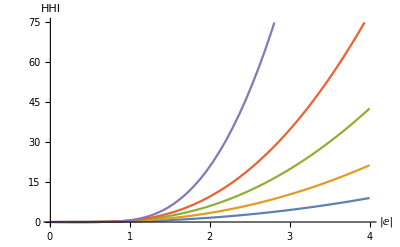

```mathematica
Clear[Q, qi]
A:=1
c[i_]:=i
Qstar:=Q/.Solve[n-Q^ϵ/A∑_(i=1)^n c[i]==1/ϵ,Q][[1]]
qstar:=q/.Solve[1-Q^ϵ/A c[i]==(q/Q)/ϵ/.{Q->((A (n-1/ϵ))/(∑_(i=1)^n c[i]))^(1/ϵ)},q][[1]]//Simplify
HHI[ϵ_,n_]=Sum[qstar^2/Qstar,{i,1,n}]//Simplify

Plot[{HHI[ϵ,4],HHI[ϵ,8],HHI[ϵ,16],HHI[ϵ,32],HHI[ϵ,128]},{ϵ,0.01,4},AxesLabel->{"|ⅇ|","HHI"}]
```

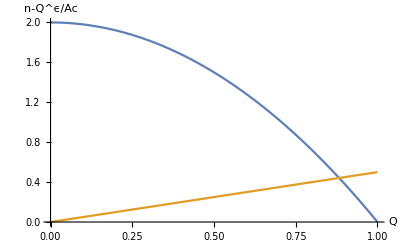

```mathematica
e:=5
Manipulate[Plot[{{n-Q^ϵ/A c},Q/ϵ},{Q,0,1}, AxesLabel->{"Q","n-Q^ϵ/Ac"}],{n,1,10},{c,0.01,100},{A,1,10},{ϵ,0.01,10}]//Simplify
```